# Exploration of the Noble gases

“Noble” something like a king between other

## Some facts about noble gases

Let’s try to see which substances we can analyse.

List of the substances in ThermodynamicData

```mathematica
substanceData=ThermodynamicData[]
```

{Acetone,Air,Ammonia,Argon,Benzene,Butane,Butene,CarbonDioxide,CarbonMonoxide,CarbonylSulfide,CisButene,Cyclohexane,Cyclopropane,Decane,Deuterium,DimethylEther,Dodecane,Ethane,Ethanol,Ethylene,Fluorine,HeavyWater,Helium,Heptane,Hexane,Hydrogen,HydrogenSulfide,Isobutane,Isobutene,Isohexane,Isopentane,Krypton,Methane,Methanol,Neon,Neopentane,Nitrogen,NitrogenTrifluoride,NitrousOxide,Nonane,Octane,Oxygen,Parahydrogen,Pentane,Perfluorobutane,Perfluoropentane,Propane,Propylene,Propyne,R11,R113,R114,R115,R116,R12,R123,R124,R125,R13,R134a,R14,R141b,R142b,R143a,R152a,R21,R218,R22,R227ea,R23,R236ea,R236fa,R245ca,R245fa,R32,R365mfc,R41,RC318,SulfurDioxide,SulfurHexafluoride,Toluene,TransButene,Trifluoroiodomethane,Water,Xenon}

We can choose the “Noble” gases among of this list with an exception as “Radon”.

Construct the list of noble gases:

```mathematica
nobleGases={"Helium","Neon","Argon","Krypton","Xenon"};
```

We can try to analyze properties of noble gases

Extraction of data from ThermodynamicData about noble gases

```mathematica
properties=DeleteMissing[ThermodynamicData[#]]&/@nobleGases;
```

Construct the array of properties

```mathematica
data=Transpose[{Keys[properties]⟦1⟧,Values[properties⟦1⟧],Values[properties⟦2⟧],Values[properties⟦3⟧],Values[properties⟦4⟧],Values[properties⟦5⟧]}];
```

Construct the grids of properties

```mathematica
Grid[Prepend[data⟦1;;6⟧,data⟦20⟧],Frame->All]
Grid[Prepend[data⟦7;;12⟧,data⟦20⟧],Frame->All]
Grid[Prepend[data⟦13;;19⟧,data⟦20⟧],Frame->All]
Grid[Prepend[data⟦22;;25⟧,data⟦20⟧],Frame->All]
Grid[Prepend[data⟦26;;All⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton | xenon
CriticalDensity | 69.6412 kg/m^3 | 481.915 kg/m^3 | 535.6 kg/m^3 | 909.208 kg/m^3 | 1102.86 kg/m^3
CriticalEnthalpy | 11869.8 J/kg | 59461. J/kg | -4331.55 J/kg | 76278.5 J/kg | 68074.8 J/kg
CriticalEntropy | 2183.29 J/(kg K) | 1502.21 J/(kg K) | 2247.64 J/(kg K) | 424.449 J/(kg K) | 274.76 J/(kg K)
CriticalInternalEnergy | 8619.35 J/kg | 53902.7 J/kg | -13411.1 J/kg | 70201.2 J/kg | 62777.7 J/kg
CriticalPressure | 227460. Pa | 2.6786×10^6 Pa | 4.863×10^6 Pa | 5.525×10^6 Pa | 5.842×10^6 Pa
CriticalTemperature | 5.1953 K | 44.4918 K | 150.687 K | 209.48 K | 289.733 K

Name | helium | neon | argon | krypton | xenon
Density | 0.166317 kg/m^3 | 0.838471 kg/m^3 | 1.66182 kg/m^3 | 3.49123 kg/m^3 | 5.48851 kg/m^3
Enthalpy | 1.52789×10^6 J/kg | 361621. J/kg | 152325. J/kg | 151069. J/kg | 116595. J/kg
Entropy | 27879.3 J/(kg K) | 5661.71 J/(kg K) | 3864.12 J/(kg K) | 1122.6 J/(kg K) | 673.685 J/(kg K)
InternalEnergy | 918658. J/kg | 240776. J/kg | 91353.2 J/kg | 122046. J/kg | 98133.4 J/kg
IsobaricHeatCapacity | 5192.99 J/(kg K) | 1030.37 J/(kg K) | 521.608 J/(kg K) | 249.257 J/(kg K) | 160.185 J/(kg K)
IsochoricHeatCapacity | 3116.03 J/(kg K) | 618.144 J/(kg K) | 312.398 J/(kg K) | 149.039 J/(kg K) | 95.4761 J/(kg K)

Name | helium | neon | argon | krypton | xenon
MolarDensity | 41.5522 mol/m^3 | 41.5517 mol/m^3 | 41.5996 mol/m^3 | 41.6625 mol/m^3 | 41.8036 mol/m^3
MolarEnthalpy | 6115.52 J/mol | 7297.15 J/mol | 6085.1 J/mol | 12659.3 J/mol | 15308.1 J/mol
MolarEntropy | 111.59 J/(K mol) | 114.248 J/(K mol) | 154.364 J/(K mol) | 94.0719 J/(K mol) | 88.4501 J/(K mol)
MolarInternalEnergy | 3677.02 J/mol | 4858.62 J/mol | 3649.38 J/mol | 10227.2 J/mol | 12884.2 J/mol
MolarIsobaricHeatCapacity | 20.7855 J/(mol K) | 20.7918 J/(mol K) | 20.8372 J/(mol K) | 20.8872 J/(mol K) | 21.0312 J/(mol K)
MolarIsochoricHeatCapacity | 12.4722 J/(mol K) | 12.4735 J/(mol K) | 12.4797 J/(mol K) | 12.4892 J/(mol K) | 12.5353 J/(mol K)
MolarSpecificVolume | 0.0240661 m^3/kg | 0.0240664 m^3/kg | 0.0240387 m^3/kg | 0.0240024 m^3/kg | 0.0239214 m^3/kg

Name | helium | neon | argon | krypton | xenon
SoundSpeed | 1007.86 m/s | 448.922 m/s | 318.959 m/s | 220.072 m/s | 175.501 m/s
SpecificVolume | 6.01262 m^3/kg | 1.19265 m^3/kg | 0.60175 m^3/kg | 0.286432 m^3/kg | 0.182199 m^3/kg
ThermalConductivity | 0.153505 W/(m K) | 0.0475569 W/(m K) | 0.0174963 W/(m K) | 0.00922286 W/(m K) | 0.00545022 W/(m K)
TriplePointGasDensity | 1.14551 kg/m^3 | 4.44453 kg/m^3 | 4.05458 kg/m^3 | 6.57099 kg/m^3 | 8.22265 kg/m^3

Name | helium | neon | argon | krypton | xenon
TriplePointLiquidDensity | 146.242 kg/m^3 | 1252.28 kg/m^3 | 1416.75 kg/m^3 | 2446.9 kg/m^3 | 2965.9 kg/m^3
TriplePointPressure | 4856.5 Pa | 43464. Pa | 68891. Pa | 73500. Pa | 81770. Pa
TriplePointTemperature | 2.1768 K | 24.556 K | 83.8058 K | 115.775 K | 161.405 K
Viscosity | 0.0000196176 s Pa | 0.0000307712 s Pa | 0.0000223065 s Pa | 0.0000247551 s Pa | 0.0000226315 s Pa

## Analysing of the density functions

Let’s try to analyse Density of noble gases under pressure with constant temperature

Construct the array of pressure, density data for plot

```mathematica
densitydata=Transpose[
{Quantity[Range[1,100,2]1000,"Pascals"],UnitSimplify@ThermodynamicData[#,"Density",{"Temperature"->Quantity[20,"DegreesCelsius"],"Pressure"->Quantity[Range[1,100,2]1000,"Pascals"]}]}]&/@nobleGases;
```

Plot the density function with constant temperature at 50 C°

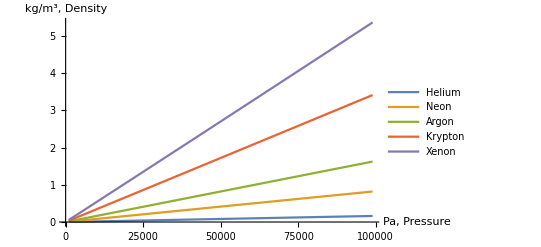

```mathematica
ListLinePlot[densitydata
,AxesLabel->{"Pa, Pressure","kg/m^3, Density"}
,PlotLegends->nobleGases]
```

As we see, density become zero value at zero point because of state of substance. Let’s try do the same with constant atmospheric pressure.

Constructing data for plot

```mathematica
densitydata2=Transpose[
{Quantity[Range[100,400,10],"Kelvins"],UnitSimplify@ThermodynamicData[#,"Density",{"Pressure"->Quantity[20,"Pascals"],"Temperature"->Quantity[Range[100,400,10],"Kelvins"]}]}]&/@nobleGases;
```

Plot the data

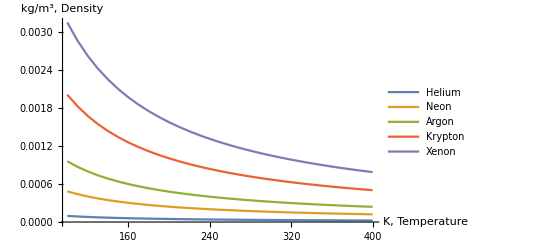

```mathematica
ListLinePlot[densitydata2
,AxesLabel->{"K, Temperature","kg/m^3, Density"}
,PlotLegends->nobleGases]
```

As we see, shape of density functions are similar. And we also see that them don’t become liquid at very low temperature. Let’s try to convert Kelvins to Degree of Celcius

Convert Kelvins to Celcius

```mathematica
N@UnitConvert[Quantity[100,"Kelvins"],"DegreesCelsius"]
```

-173.15 °C

## Phase plotting

Lets try to do very interesting thing: we will try to build phase plots of each noble gases

Choosing the pressure interval

```mathematica
pressures=Quantity[Table[10^x,{x,-6,12,0.3}],"Pascals"];
```

Create a phase plot for each noble gas

```mathematica
phaseplots=ListLogPlot[
Transpose[
{#,pressures}
]&
/@
{ThermodynamicData[#,"LiquidVaporPhaseBoundary",{"Pressure"->pressures}],
ThermodynamicData[#,"SolidLiquidPhaseBoundary",{"Pressure"->pressures}],
ThermodynamicData[#,"SolidVaporPhaseBoundary",{"Pressure"->pressures}]},
PlotRange->All,
Joined->True,
Frame->True,
FrameLabel->{"K, Temperature","Pa, Pressure"},
PlotLegends->{"Vapor Liquid","Solid Liquid","Solid Vapor"},
GridLines->Automatic,
ImageSize->Medium]&/@nobleGases;
```

Construct the grid of this plots

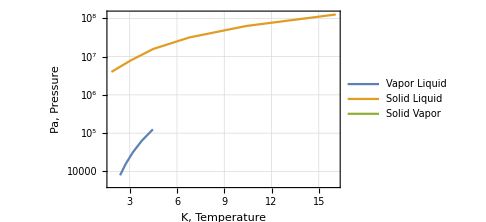
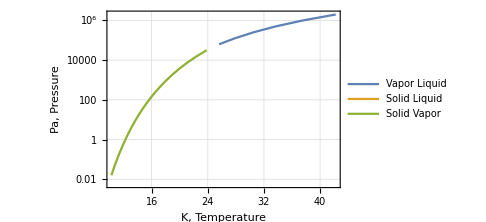
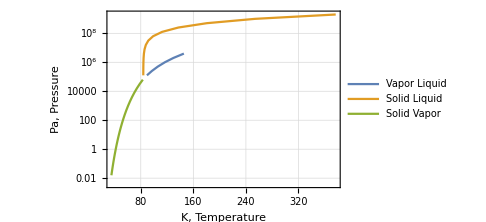
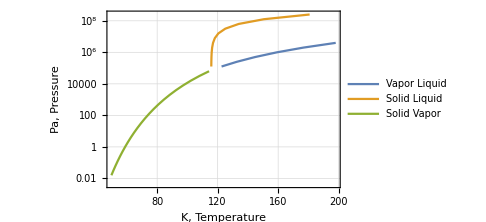
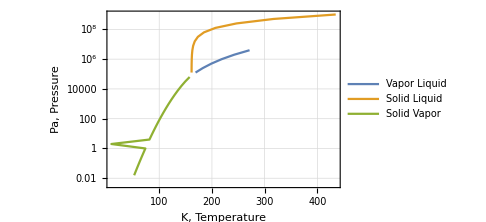
Helium | -Graphics-
Neon | -Graphics-
Argon | -Graphics-
Krypton | -Graphics-
Xenon | -Graphics-

```mathematica
Grid[Transpose[{nobleGases,phaseplots}]]
```

## Phase plot analysing

Let’s try to analyse the vapor-liquid phase boundary

Constructing the array of data near the vapor-liquid boundary with constant pressure

```mathematica
data=Transpose[{Quantity[Table[x,{x,1,200,10}],"Kelvins"],ThermodynamicData[#,"Density",{"Temperature"->Quantity[Table[x,{x,1,200,10}],"Kelvins"],"Pressure"->Quantity[10^6,"Pascals"]}]}]&/@nobleGases;
```

Constructing the array of data near the vapor-liquid boundary with constant temperature

```mathematica
datap=Transpose[{Quantity[Table[10^5*i,{i,1,10}],"Pascals"],ThermodynamicData[#,"Density",{"Temperature"->Quantity[200,"Kelvins"],"Pressure"->Quantity[Table[10^i,{i,1,10}],"Pascals"]}]}]&/@nobleGases;
```

Constructing the grid of plots

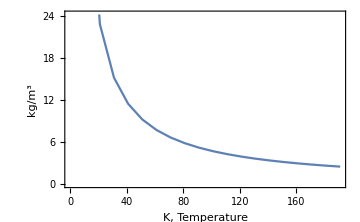
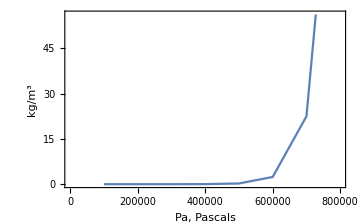
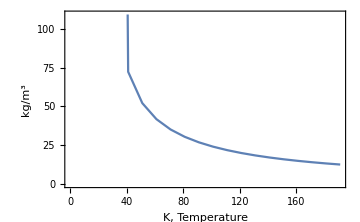
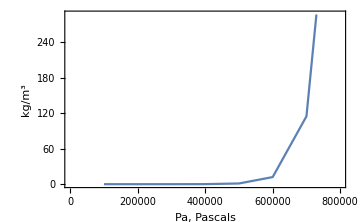
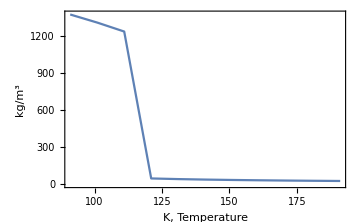
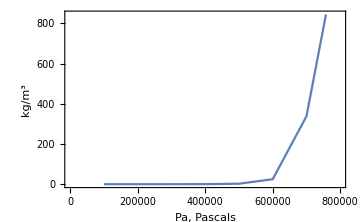
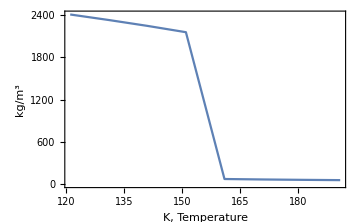
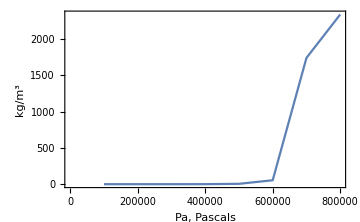
Helium | -Graphics- | -Graphics-
Neon | -Graphics- | -Graphics-
Argon | -Graphics- | -Graphics-
Krypton | -Graphics- | -Graphics-
Xenon | -Graphics- | -Graphics-

```mathematica
Grid[Table[{nobleGases[[i]],ListLinePlot[data[[i]],Axes->False,Frame->True,FrameLabel->{"K, Temperature","kg/m^3"},ImageSize->Medium],ListLinePlot[datap[[i]],Axes->False,Frame->True,FrameLabel->{"Pa, Pascals","kg/m^3"},ImageSize->Medium]},{i,1,Length[nobleGases]}]]
```

We can see discontinuity of density function in interval of extremely low temperatures. It is proof of existing the process of phase transition.

## The speed of sound in noble gases

We can describe this interesting parameters by using different formulas, we can count noble gases as ideal gases because of it atomic structure

Extracting the necessary formula from FormulaData[]

```mathematica
FormulaData[{"IdealGasSpeedOfSoundTemperature","MolarGasConstant"}]
FormulaData[{"IdealGasSpeedOfSoundPressure","Density"}]
```

v_s Speed==√(((1 R) T Temperature γ Unitless)/(M MolarMass))

v_s Speed==√((P Pressure γ Unitless)/(d MassDensity))

Let’s look at the parameters which control the value of sound speed

```mathematica
Grid[{FormulaData[{"IdealGasSpeedOfSoundTemperature","MolarGasConstant"},#],
FormulaData[{"IdealGasSpeedOfSoundPressure","Density"},#]}&["QuantityVariableNames"]]
```

v_s Speed→speed of sound | M MolarMass→molar mass | T Temperature→temperature | γ Unitless→adiabatic index
v_s Speed→speed of sound | d MassDensity→density | P Pressure→pressure | γ Unitless→adiabatic index

Let’s try to use EntityData about our gases

Extraction of the properties of noble gases

```mathematica
nobleentity=LinguisticAssistant;
```

Searching the values of necessary properties

```mathematica
nobleentity["Name"]
```

{helium,neon,argon,krypton,xenon,radon,oganesson}

We see that Entity have more information about noble gases than Thermodynamic. Let’s try to analyse our gases: helium, neon, argon, xenon and krypton.

Extraction molar mass

```mathematica
nobleentity["MolarMass"][[1;;5]]
```

{4.002602 g/mol,20.1791 g/mol,39.948 g/mol,83.798 g/mol,131.293 g/mol}

Extraction adiabatic index

```mathematica
nobleentity["AdiabaticIndex"][[1;;5]]
```

{5/3,5/3,5/3,5/3,5/3}

Adiabatic Index of all our gases is equal to adiabatic index of ideal gas, so we can use the formulas! Let’s try to do this, we must remember that density is an function of pressure and temperature.

Finding the speed of sound in helium at 273 Kelvins

```mathematica
FormulaData[{"IdealGasSpeedOfSoundTemperature","MolarGasConstant"},{"γ"->5/3,"M"->nobleentity["MolarMass"][[1]],"T"->Quantity[273,"Kelvins"]}]
```

v_s Speed==972.191 m/s

For building the plot we must transform it to function:

Constructing the function of speed

```mathematica
velocitytemp[temp_]:=FormulaData[{"IdealGasSpeedOfSoundTemperature","MolarGasConstant"},{"γ"->5/3,"M"->nobleentity["MolarMass"][[#]],"T"->Quantity[temp,"Kelvins"]}][[2]]&/@Range[5]
```

```mathematica
velocitytemp[100][[1]]
```

588.397 m/s

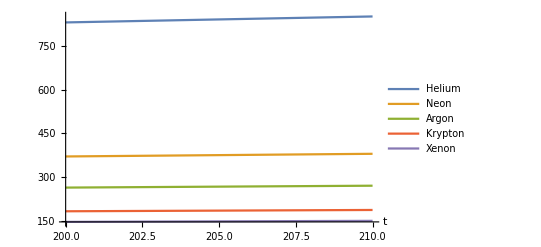

```mathematica
Plot[{velocitytemp[t][[1]],velocitytemp[t][[2]],velocitytemp[t][[3]],velocitytemp[t][[4]],velocitytemp[t][[5]]},{t,200,210},PlotLegends->nobleGases,AxesLabel->Automatic]
```

```mathematica
velocitypres[pres_]:=FormulaData[{"IdealGasSpeedOfSoundPressure","Density"},{"γ"->5/3,"d"->ThermodynamicData[nobleGases[[#]],"Density",{"Temperature"->Quantity[293,"Kelvins"],"Pressure"->Quantity[pres,"Pascals"]}],"P"->Quantity[pres,"Pascals"]}][[2]]&/@Range[5]
```

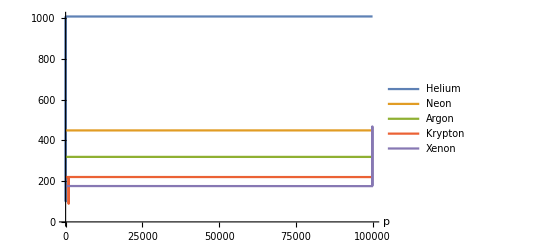

```mathematica
Plot[{velocitypres[p][[1]],velocitypres[p][[2]],velocitypres[p][[3]],velocitypres[p][[4]],velocitypres[p][[5]]},{p,10,10^5},PlotLegends->nobleGases,AxesLabel->Automatic]
```

Further Explorations

Analysing of other kinds of gases like halogens

Analysing of another properties of substances

Authorship information

Andrey Krotkikh

6/21/2017

andrei.krotkih@gmail.com